## Einleitung

Dieses package ist die Weiterentwicklung des alten SimpleHUPhysicsPractical` für das Grundpraktikum der Physik an der HU.
Es ist deutlich besser und angenehmer zu benutzen als das alte und hoffentlich hilft es euch noch mehr als das alte ^^
Wie immer gilt, dass ihr Fehler bei meiner Email melden könnt. Es gilt vorallem, dass ich dieses Package noch nicht so ausgiebig testen konnte wie das Alte also deckt mich zu ^^ 
Schaut auch hin und wieder mal, ob Updates vorhanden sind.

Julien.Kluge@gmail.com

## Installation

#### Zur Installation, müsst ihr nur die folgende Zeile ausführen. Hat alles geklappt, wird folgendes ausgegeben:

Installiert!

____________________________________________________________________________________

```mathematica
If[Floor[$VersionNumber]<11,Print[Style["Das Package funktioniert nur auf Mathematica 11 oder höher!",{FontColor->Red,FontSize->16}]],
If[FileExistsQ[FileNameJoin[{NotebookDirectory[],"HUPP.m"}]],
If[DirectoryQ[$UserBaseDirectory],
Block[{endDir=FileNameJoin[{$UserBaseDirectory,"Applications"}]},
If[Not@DirectoryQ[endDir],Print[endDir<>" existiert nicht. Es wird erstellt..."];CreateDirectory[endDir]];
If[FileExistsQ[FileNameJoin[{endDir,"HUPP.m"}]],Print["HUPP.m existiert bereits. Es wird überschrieben..."];DeleteFile[FileNameJoin[{endDir,"HUPP.m"}]]];
CopyFile[FileNameJoin[{NotebookDirectory[],"HUPP.m"}],FileNameJoin[{endDir,"HUPP.m"}]];
Print[Style["Installiert!",{FontSize->16,FontColor->Darker[Green],FontWeight->Bold}]];
];
,Print["Es existiert kein vorhandener User-Base-Pfad"]]
,Print["HUPP.m nicht gefunden!"]]
];
```

### Nach der Installation: Computer neu starten!

#### Optional: Load-Befehl

Optional könnt ihr zusätzlich auch folgenden Code ausführen, der euch den Befehl HUPP[] in Mathematica einfügt. So könnt ihr das Package deutlich bequemer laden.

```mathematica
If[DirectoryQ[FileNameJoin[{$UserBaseDirectory,"Kernel"}]],
If[FileExistsQ[FileNameJoin[{$UserBaseDirectory,"Kernel","init.m"}]],
Block[{fileContent=ReadString[FileNameJoin[{$UserBaseDirectory,"Kernel","init.m"}]],fileStream},
If[StringContainsQ[fileContent,"HUPP[]:="],Print["Das init.m File enthält bereits eine Definition des HUPP[] Befehls"],
fileStream=OpenAppend[FileNameJoin[{$UserBaseDirectory,"Kernel","init.m"}]];
WriteString[fileStream,"\n\nHUPP[]:=(ClearAll[\"HUPP`*\"];Needs[\"HUPP`\"])\n"];
Close[fileStream];
Print[Style["Befehl hinzugefügt!",{FontSize->16,FontColor->Darker[Green],FontWeight->Bold}]];
];
];
,Print["Die Kernel initialization Datei existiert nicht."]];
,Print["Der Kernelpfad existiert nicht."]];
```

## Laden

Um das Package zu laden, muss der Needs[] Befehl ausgeführt werden. (Ignoriert hier mal das ClearAll[])

```mathematica
ClearAll["HUPP`*"]

Needs["HUPP`"]
```

Es muss auf Groß/Kleinschreibung geachtet werden und dass es auf das Gravis Zeichen (`) endet.

### Oder Alternativ mit Befehl

```mathematica
HUPP[]
```

## HUPPHelp

Der erste Befehl listet alle Befehle und Optionen des Packages auf :

```mathematica
?HUPPHelp
```

```mathematica
HUPPHelp[]
```

## PythagoreanSum

```mathematica
?PythagoreanSum
```

Wie der Name schon sagt, lässt sich mit diesem Befehl pythagoräisch addieren.
Beispielsweise :

```mathematica
PythagoreanSum[a,b,c]
```

Dabei nimmt der Befehl auch Listen entgegen und ignoriert verschachtelungen :

```mathematica
PythagoreanSum[{a,b,{c,{d}}}]
```

```mathematica
PythagoreanSum[{a,{a},b}]
```

## ConfidenceSigma & InverseConfidenceSigma

```mathematica
?ConfidenceSigma
```

ConfidenceSigma rechnet Standardabweichungen in statistische Wahrscheinlichkeit um

```mathematica
ConfidenceSigma[1.0]
```

Dabei gilt mit Vorsicht, dass exakte Argumente auch exakt ausgewertet werden :

```mathematica
ConfidenceSigma[2]
N[ConfidenceSigma[2]]
```

```mathematica
?InverseConfidenceSigma
```

InverseConfidenceSigma ist die Umkehrfunktion zu ConfidenceSigma. Es berechnet also statistische Prozent in Standardabweichungen um.

```mathematica
InverseConfidenceSigma[0.9545]
```

```mathematica
InverseConfidenceSigma[ConfidenceSigma[3.0]]
```

## ErrorMean

```mathematica
?ErrorMean
```

In der einfachen Variante berechnet ErrorMean den Mittelwert von Unsicherheiten (pytagoräische Addition durch anzahl der Werte)

```mathematica
ErrorMean[{a,b,c}]
```

```mathematica
ErrorMean[{5,6,7,8,7,6,5}]
```

In der Doppellistenvariante berechnet ErrorMean den Mittelwert der Werte v_i und der Unsicherheiten e_i aus.

```mathematica
ErrorMean[{{5,0.5},{6,0.4},{5.2,0.45}}]
```

## StudentTValue

```mathematica
?StudentTValue
```

Wie der Name schon vermuten lässt, berechnet StudentTValue den Student - T Wert dür die Freiheitsgrade und optional auch Standardabweichungen.

ACHTUNG: Der Befehl nimmt nur Ganzzahlargumente. Das führt zu einer exakten Auswertung, die eine seltsame Darstellung hat:

```mathematica
StudentTValue[15]
```

Das lässt sich aber leicht numerisch berechnen :

```mathematica
N[StudentTValue[15]]
```

In zwei Standardabweichungen :

```mathematica
StudentTValue[15,2]//N
```

Da σ nicht exakt sein muss, lässt sich hier auch die numerische Auswertung erzwingen.

```mathematica
StudentTValue[15,2.0]
```

## ConfidenceInterval & ConfidenceIntervalHU

```mathematica
?ConfidenceInterval
```

ConfidenceInterval berechnet den, mit dem Student - T Wert skalierten, Vertrauensbereich.

s̄=t·s/(√n)

```mathematica
ConfidenceInterval[{5.1,5.0,4.9,4.8,5.05,5.1}]
```

```mathematica
?ConfidenceIntervalHU
```

ConfidenceIntervalHU berechnet den Vertrauensbereich, wie er im HU Physik Praktikum definiert wurde.

s̄=Piecewise[{{s/(√n), n≥6}, {max_i |x̄-x_i|, n<6}}]

```mathematica
ConfidenceIntervalHU[{5.1,5.0,4.9,4.8,5.05,5.1}]
```

```mathematica
ConfidenceIntervalHU[{5.1,5.0,4.9,4.8,5.05}]
```

Eine Beispielsberechnung zwischen ConfidenceInterval und ConfidenceIntervalHU

```mathematica
data=RandomVariate[NormalDistribution[0,1],50]; (*zufällige Daten erzeugen*)
ListLinePlot[Transpose[{ConfidenceInterval[data[[1;;#]]],ConfidenceIntervalHU[data[[1;;#]]]}&/@Range[3,50]],PlotRange->All,PlotTheme->"Detailed",ImageSize->Large,PlotLegends->{"ConfidenceInterval","ConfidenceIntervalHU"}]
```

## CalculateMeasurement & CalculateMeasurementHU

```mathematica
?CalculateMeasurement
```

```mathematica
?CalculateMeasurementHU
```

CalculateMeasurement ist die drittwichtigste Funktion in diesem Package (zumindest meiner Meinung nach).
Es berechnet einen Messwert unter voller Berechnung der angegebenen Unsicherheiten, der statistischen Unsicherheit (Vertrauensbereich) und evtl. dem systematischen Fehler.
Aber fangen wir kleinschrittig an:

Die kleinste Form des Befehls nimmt nur Messwerte entgegen, berechnet den Mittelwert und nur die statistische Unsicherheit (Vertrauensbereich).

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1}]
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{}]
```

Man kann in der zweiten Liste nun eine konstante Unsicherheit einführen (z.B. Ableseunsicherheit) .
Hier eine konstante Unsicherheit von 0.5:

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5}]
```

Gleiches Beispiel, mehrere Unsicherheiten (0.5,1.5,0.75):

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5,1.5,0.75}]
```

Manche Unsicherheiten, wie zum Beispiel Geräteunsicherheiten von digitalen Messgeräten, haben eine Prozentangabe vom gemessenen Mittelwert. Dieser kann in der Liste mit dem Wert C angeben werden.
Zum Beispiel: (konste Unsicherheit: 0.5 - Geräteunsicherheit: 0.4+1%·x̄)

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5,0.4+0.01*C}]
```

Man kann mit diesem Befehl ebenfalls einen systematische Fehler korrigieren lassen.
Zum Beispiel: u_sys=+0.6

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5,0.4+0.01*C},+0.6]
```

CalculateMeasurement ist ebenfalls der erste Befehl, mit der Analyse - Option, die eine genau Analyse der Daten anfertigt, die wichtig sind :

```mathematica
CalculateMeasurement[{5.1,5.0,4.9,4.8,5.05,5.1},{0.5,0.4+0.01*C},+0.6,Analyze->True]
```

CalculateMeasurementHU ist der äquivalente Befehl, der die Definition des Vertrauensbereichs des HU Physik Praktikums benutzt.

## WeightedMean

```mathematica
?WeightedMean
```

Dieser Befehl führt ein gewichtetes Mittel durch. Dabei muss dem Befehl eine Liste übergeben werden. Jedes Element dieser Liste ist wiederrum eine Liste mit zwei Einträgen. Der erste Eintrag ist der Wert, der zweite die zugeordnete Unsicherheit.
Beispiel:

g_1=(9.81±0.03)m/s^2
g_2=(9.79±0.11)m/s^2
g_3=(9.80±0.04)m/s^2
g_4=(9.6±0.7)m/s^2

```mathematica
WeightedMean[{{9.81,0.03},{9.79,0.11},{9.80,0.04},{9.6,0.7}}]
```

Der Befehl warnt euch, wenn sich die Unsicherheitsintervalle nicht überschneiden :

```mathematica
WeightedMean[{{9.81,0.03},{9.59,0.11},{9.80,0.04},{9.6,0.7}}]
```

Auch dieser Befehl kennt die Analyse option :

```mathematica
WeightedMean[{{9.81,0.03},{9.79,0.11},{9.80,0.04},{9.6,0.7}},Analyze->True]
```

## RoundedErrorForm

```mathematica
?RoundedErrorForm
```

RoundedErrorForm berechnet die gerundete Darstellung eines Wertes mit seiner Unsicherheit. Er achtet dabei auf signifikante Stellen und DIN. Die Ausgabe erfolgt standartmäßig als String.

```mathematica
RoundedErrorForm[145.34,4.6]
```

```mathematica
RoundedErrorForm[0.04567,0.00279]
```

Die Ausgabe kann in eine Liste mit numerischen Werten erfolgen:

```mathematica
RoundedErrorForm[0.04567,0.00279,Form->Null]
RoundedErrorForm[0.04567,0.00279,Form->Null]//N
```

Der Befehl kann auch LaTeX code ausgeben :

```mathematica
RoundedErrorForm[0.04567,0.00279,Form->"latex"]
```

## ErrorProbability

```mathematica
?ErrorProbability
```

ErrorProbability berechnet die Irrtumswahrscheinlichkeit aus den χ^2-Test und den Freiheitsgraden

```mathematica
ErrorProbability[10,2.56]
ErrorProbability[8,7.34]
```

Exakte Argumente werden auch exakt ausgewertet:

```mathematica
ErrorProbability[20,3]
```

## GaussianErrorPropagation

```mathematica
?GaussianErrorPropagation
```

Der zweitwichtigste Befehl in diesem Package. Die automatische Gaußsche Fehlerfortpflanzung.
In der einfachsten Darstellung, berechnet der Befehl nur die Formel.

```mathematica
GaussianErrorPropagation[a*x/c+d]
```

Im zweiten Argument, listet man die Variablen mit ihren Werten und Unsicherheiten auf.

a=(50.0±0.1)
d=(8.1±0.9)

```mathematica
GaussianErrorPropagation[a/d,{{a,50,0.1},{d,8.1,0.9}}]
```

Kovarianzen zwischen Variablen werden in einer Liste mit den zwei Variablen und der Kovarianc angegeben.

u_(a,d)=0.5

```mathematica
GaussianErrorPropagation[a/d,{{a,50,0.1},{d,8.1,0.9},{a,d,0.5}}]
```

Keine der Listen muss völlig ausgefüllt sein (beachte, dass x keine Unsicherheitsbehaftet größe ist, wenn sie nicht explizit angegeben wird):

```mathematica
GaussianErrorPropagation[a*x/c+d,{a,{d,1},{c,5,0.1},{a,c},{a,d,0.5}}]
```

Auch dieser Befehl, kennt die Analyse Option.

```mathematica
GaussianErrorPropagation[a/d,{{a,50,0.1},{d,8.1,0.9},{a,d,0.5}},Analyze->True]
```

Der Befehl ist ebenfalls in der Lage, Daten aus FittedModel - Objekten zu ziehen.
Dazu müssen zu allererst fits erstellt werden.

```mathematica
data=Table[{x,-20*x^2-x+1+RandomReal[]},{x,0,10,0.5}];
linearFit=LinearModelFit[data,{x^2,x,1},x]
nonlinearFit=NonlinearModelFit[data,a*x^2+b*x+c,{a,b,c},x]
```

Wie erklärt, erstellt Mathematica bei jedem Fit, ein FittedModel - Objekt. Dabei ist wichtig anzumerken :
LINEARE FITS UND NICHTLINEARE FITS ERZUEGEN UNTERSCHIEDLICHE FITTEDMODEL - OBJEKTE
Ich halte es kurz und sage nur, dass in Nichtlinearen-FittedModel-Objekte Informationen über Variablennamen halten.
Dadurch kann der Befehl leicht diese Objekte benutzen.
Es werden sämtliche Variablen und Kovarianzen berücksichtigt.

```mathematica
GaussianErrorPropagation[a/b+c,{nonlinearFit}]
```

Bei linearen fits, muss noch die Variablenstruktur mit angegeben werden :

```mathematica
GaussianErrorPropagation[a/b+c,{{linearFit,{a,b,c}}}]
```

Das kann natürlich auch gemischt angewendet werden.

```mathematica
GaussianErrorPropagation[a/b+c^d,{nonlinearFit,{d,2,0.1}}]
```

Und auch analysiert werden

```mathematica
GaussianErrorPropagation[a/b+c^d,{nonlinearFit,{d,2,0.1}},Analyze->True]
```

## AdaptiveNonlinearModelFit

```mathematica
?AdaptiveNonlinearModelFit
```

Um einen nichtlinearen Fit in Mathematica auszuführen, benutzt man den Befehl NonlinearModelFit.
Wie aber für nichtlineare Fits üblich, besteht die Gefahr, dass diese Fits bei ungeeigneter Wahl der Startparameter nicht konvergieren. 
Nun wäre es aber wünschenswert wenn die Funktion selbstständig Startparameter wählen könnte um den Fit zu begünstigen. 
Dafür enthält dieses package den Befehl AdaptiveNonlinearModelFit. Die Syntax ist die gleiche wie beim normalen NonlinearModelFit.

#### Achtung:

Dieser Befehl ist experimentell. Ich habe eine lange Zeit verbracht die Methoden für diesen Befehl zu generalisieren sodass sie möglichst viele Fitmodelle verarbeiten könnten. Trotzdem ist das kein Garant dafür, dass der Fit konvergiert.
Desweiteren muss beachtet werden, dass der Befehl im inneren massive Algebraische Operationen ausführt. Demnach kann es sein, dass diese Funktion mehrere Sekunden, Minuten oder sogar länger braucht. Die längste gemessene Zeit dieser Funktion liegt bei ungefähr 10Minuten für ein Fitmodell mit 6 Parametern zur Bestimmung der Autokorrelationsfunktion einer Quantenkorrelation. Üblich sind aber nur 2-3 Sekunden für einfachere Modelle.
Trotzdem: seit bereit nichtsdestotrotz selber Startwerte für komplizierte Probleme bereitzustellen.

Zum testen erstellen wir drei Test-Datensätze (die natürlich so von mir gewählt worden sind, dass NonlinearModelFit ohne Wahl der Startparameter nicht konvergiert):

```mathematica
adata1={{1,10001.8},{2,10000.8},{3,9999.89},{4,9999.53},{5,9999.73},{6,10000.1},{7,10000.3},{8,10000.2},{9,9999.89},{10,9999.8},{11,9999.91},{12,10000.1},{13,10000.2},{14,10000.1},{15,9999.9},{16,9999.88},{17,9999.99},{18,10000.1},{19,10000.1},{20,10000.},{21,9999.92},{22,9999.92},{23,10000.},{24,10000.1},{25,10000.1},{26,9999.97},{27,9999.92},{28,9999.95},{29,10000.},{30,10000.1}};
adata2={{-3.01,-33},{-2.6,-34},{-2.2,-33},{-1.8,-26},{-1.7,-20},{-1.6,-12},{-1.5,0},{-1.4,20},{-1.3,61}};
wdata2={6.98467,14.3664,6.90228,5.30757,4.61407,6.94984,14.9547,14.4406,3.68319};
adata3=(#+{0,10000}&)/@{{0.1,0.0898647},{0.2,-0.0535735},{0.3,-0.148313},{0.4,0.0846445},{0.5,0.09901},{0.6,-0.074521},{0.7,-0.142624},{0.8,-0.0864354},{0.9,-0.0212738},{1.,0.0221625},{1.1,0.105401},{1.2,-0.0966202},{1.3,0.0877835},{1.4,0.0789275},{1.5,0.015885},{1.6,0.118934},{1.7,0.04146},{1.8,0.0344122},{1.9,0.054369},{2.,0.127307},{2.1,0.120975},{2.2,0.0272045},{2.3,0.102872},{2.4,0.11786},{2.5,-0.122479},{2.6,-0.109226},{2.7,-0.110917},{2.8,0.0986023},{2.9,-0.0694651},{3.,0.084825},{3.1,0.0369083},{3.2,0.197759},{3.3,0.138431},{3.4,0.321953},{3.5,0.360677},{3.6,0.27348},{3.7,0.441175},{3.8,0.407004},{3.9,0.359329},{4.,0.418597},{4.1,0.552704},{4.2,0.525389},{4.3,0.528137},{4.4,0.224216},{4.5,0.436397},{4.6,0.389716},{4.7,0.326866},{4.8,0.108578},{4.9,0.225344},{5.,0.0938303}};
```

#### Beispieldatensatz 1: versetzte, abklingende Schwingung

Dieser Datensatz konvergiert in beiden Fällen. AdaptiveNonlinearModelFit kann aber von Anfang an, den c-Parameter wählen, wodurch die anderen Parameter nichtmehr groß schwanken müssen um ins globale Minimum zu konvergieren.
NonlinearModelFit hingegen braucht sehr viele Schritte bis der c-Parameter angepasst ist wodurch die Parameter a und b weit driften und die Funktion somit in ein lokales Minimum konvergiert welches, wie im Plot zu sehen, aber eine viel zu große Frequenz aufweist.

```mathematica
fit1=NonlinearModelFit[adata1,a*Sin[b*x]/x+c,{a,b,c},x];
afit1=AdaptiveNonlinearModelFit[adata1,a*Sin[b*x]/x+c,{a,b,c},x];
Show[ListPlot[adata1,PlotRange->All,PlotStyle->Black],Plot[Evaluate@{fit1["BestFit"],afit1["BestFit"]},{x,1,30},PlotRange->All,PlotLegends->{"NonlinearModelFit","AdaptiveNonlinearModelFit"}]]
```

#### Beispieldatensatz 2: Photostrom im äußeren Photoeffekt

Dies ist ein Realer Datensatz vom Versuch A1-Photoeffekt. Man sieht leicht, dass NonlinearModelFit sich in einem lokalen Minimum gefangen hat, dass realisiert und eine Fehlermeldung ausgibt. 
AdaptiveNonlinearModelFit kann von Anfang an aber a und b wählen wodurch nurnoch c gefunden werden muss.

```mathematica
fit2=NonlinearModelFit[adata2,a*(Exp[(u-b)/c]-1),{a,b,c},u,Weights->1/wdata2^2,MaxIterations->10000];
afit2=AdaptiveNonlinearModelFit[adata2,a*(Exp[(u-b)/c]-1),{a,b,c},u,Weights->1/wdata2^2];
Show[ListPlot[adata2,PlotRange->All,PlotStyle->Black],Plot[Evaluate@{fit2["BestFit"],afit2["BestFit"]},{u,-3,-1},PlotRange->All,PlotLegends->{"NonlinearModelFit","AdaptiveNonlinearModelFit"}]]
```

#### Beispieldatensatz 3: verschobene Normalverteilung mit stark rauschenden Daten

Auch hier merkt NonlinearModelFit, dass es nicht konvergiert ist aber dagegen nichts tun kann.
AdaptiveNonlinearModelFit kann selbst aus diesen schlechten Daten die Parameter A, x0 und o wählen wodurch nurnoch eta gefunden werden muss.

```mathematica
fit3=NonlinearModelFit[adata3,A*Exp[-(x-x0)^2/eta]+o,{A,x0,eta,o},x,MaxIterations->10000];
afit3=AdaptiveNonlinearModelFit[adata3,A*Exp[-(x-x0)^2/eta]+o,{A,x0,eta,o},x];
Show[ListPlot[adata3,PlotRange->All,PlotStyle->Black],Plot[Evaluate@{fit3["BestFit"],afit3["BestFit"]},{x,0,5},PlotRange->All,PlotLegends->{"NonlinearModelFit","AdaptiveNonlinearModelFit"}]]
```

## FitPlot

```mathematica
?FitPlot
```

#### Der Befehl, für den dieses Package überhaupt existiert. Wir erzeugen erstmal Daten.

```mathematica
n=20;
xErrors=0.05+Abs@RandomVariate[NormalDistribution[0,0.05],n];
yErrors=RandomVariate[NormalDistribution[0,0.3],n];
data=Table[{i/n*5,0.2*(i/n*5)^2-2*i/n*5+yErrors[[i]]},{i,1,n}];
yErrors=0.2+Abs@yErrors;
```

#### Nun benutzen wir den Befehl in seiner einfachsten Form:

```mathematica
FitPlot[data,a*x^2+b*x+c,x]
```

#### Mit Fehlerbalken :

```mathematica
FitPlot[data,xErrors,yErrors,a*x^2+b*x+c,x]
```

#### Und den restlichen Parametern

```mathematica
FitPlot[data,xErrors,yErrors,a*x^2+b*x+c,x,"x-Achse","y-Achse",{3.2,0.4}]
```

#### Davon kann man sich erst erschlagen fühlen, aber wir fangen es langsam an. Als erstes alle Standardparameter :

```mathematica
FitPlot[
data (*Daten die gefittet werden sollen in Punktlisten {{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},...} oder zu mehreren Fits {{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},...},{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},...},...}*)
,xErrors (*die x Fehler in Einfachlisten {Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...} oder Mehrfachlisten {{Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...},{Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...},...}*)
,yErrors (*die y Fehler in Einfachlisten {Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...} oder Mehrfachlisten {{Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...},{Subscript[u, x,1],Subscript[u, x,2],Subscript[u, x,3]...},...}*)
,equations (*die Gleichungen, nach denen gefittet wird. Wenn nur eine Gleichung gefittet wird, braucht es keine Liste*)
,variables (*die Funktionsvariablen der Gleichungen. Wird nur ein Fit gemacht, braucht es keine Liste*)
,xLabel (*das x-Achsenlabel als string also mit Anführungszeichen*)
,yLabel (*das y-Achsenlabel als string also mit Anführungszeichen*)
,legendPosition (*die Position der legende. Eine leere Liste {} stellt die Legende neben den Plot, Null entfernt sie komplett oder ein Punkt {x,y} positioniert sie mit der linken oberen Ecke in diesen Punkt*)
]
```

#### Was bedeutet nun also die Tabelle neben dem Plot? Das ist die Auswertungstabelle. Hier nochmal :

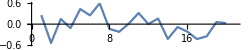
regression | 
equation | a x^2+b x+c
parameters |  | value | error | p-value | 
c | 0.167699 | 0.177309 | 0.357502 | c
b | -2.11643 | 0.134374 | 1.4236×10^-11 | b
a | 0.214673 | 0.0222668 | 2.63896×10^-8 | a
model-object | FittedModel[0.167699-2.11643 x+0.214673 x^2]
{χ^2/dof,α} | {0.295409,0.586775}
{R^2,(R̃)^2}
{R^2%,(R̃)^2%} | {0.982148,0.980048}
{86.6388,85.8747}
correlations |  | c | b | a | 
c | 1. | -0.92013 | 0.82979 | c
b | -0.92013 | 1. | -0.97583 | b
a | 0.82979 | -0.97583 | 1. | a
 | c | b | a | 
covariances |  | c | b | a | 
c | 0.0314386 | -0.0219228 | 0.0032761 | c
b | -0.0219228 | 0.0180563 | -0.00291975 | b
a | 0.0032761 | -0.00291975 | 0.000495809 | a
 | c | b | a | 
residuals | -Graphics-

#### In Reihenfolge :

regression: Als erstes sehen wir hier die Farbige Linie. Diese zeigt euch an, welche Farbe die Regression im Plot hat. 
Desweiteren findet ihr daneben noch eine Beschreibung. Möglichkeiten dafür sind: {polynomial linear, nonlinear, adaptive nonlinear, single linear, multi-combination linear}.
Diese Beschreibungen geben euch an, was der Befehl im “inneren” mit euren Fit-Modell angestellt hat. Wie ihr ja wissen solltet, kann eine Regression linear oder nichtlinear ablaufen.
Dabei gilt, dass linear immer besser ist als nichtlinear, da hier die Gefahr der nicht-Konvergenz nicht besteht. FitPlot versucht also nun euer angegebenes Fitmodell zu analysieren.
Wenn eure Gleichung ohne große Änderungen als Polynom dargstellt werden kann, dass einem linearen Fit genügt, wird eure Funktion im inneren danach umgestellt und die jeweilig nötigen
Funktionen und Parameter extrahiert und linear regressiert. Das wird dargstellt mit “polynomial linear”
single linear und multi-combination linear sind Namen für Gleichungen die als lineares Fitmodell aber nicht als Polynom dargestellt werden können. Hierbei werden aber scheinbar offensichtliche
Vereinfachungen NICHT gemacht also wenn ihr unbedingt linear fitten wollt, müsst ihr eure Gleichung selbstständig linearisieren.
nonlinear ist demnach einfach die Option bei der kein lineares Fitmodell extrahiert werden konnte und es wird nichtlinear regressiert. adaptive nonlinear benutzt den AdaptiveNonlinearModelFit dieses Packages um eine Konvergenz wahrscheinlicher zu machen.

equation: wie man sich denken kann, wird hier nochmal das Fitmodell dargstellt (nicht vereinfacht). Wenn hier eine Liste mit zwei Gleichungen angegeben wird, dann weil ein Parameter umbenannt wurde (weiteres dazu später).

parameters: Hier wird die Parameter-Tabelle dargstellt. Hier bekommt ihr euren internen Variablennamen, die Abschätzung des Wertes, der Unsicherheit, den statistischen P-Wert und den Darstellungsname der Variable.
Der P-Wert ist bei statistisch signifikanten Werten als Faustregel unter 0.05. Sollte ein Parameter das nicht erfüllen, wird die Zeile in Rot dargstellt.

model-object: Bei jeder Regression erzeugt Mathematica ein FittedModel-Objekt. Meistens unnötig für euch aber wenn ihr Zusatzinfos braucht die euch hier nicht angezeigt werden, dann daraus.

{χ^2/dof,α}: Der erste Wert der Liste ist der χ^2/dof Wert. Der zweite ist die zugehörige Irrtumswahrscheinlichkeit α. Die Farbe kann von grün (alles okay) zu orange (mäßige Irrtumswahrscheinlichkeit) bis rot (große Irrtumswahrscheinlichkeit) gehen.

{R^2,(R̄)^2}
{R^2%,(R̄)^2%} : R^2 ist der normale R-Quadrat Test und (R̄)^2 ist der angepasste Test. Die Prozentangaben darunter sind die prozentualen Erklärungen der Abweichungen zur Standardabweichung. (http://people.duke.edu/~rnau/rsquared.htm)
Auch hier ist eine Farbliche angabe von grün zu orange bis rot ein Indikator für die Erklärung der Standardabweichung (berechnet aus den erklärten Standartabweichungen des (R̄)^2%).

correlations: Korrelationsmatrix zur Abschätzung der Korrelationen

covariances: Kovarianzmatrix für die korrelierte Gaußsche Fehlerfortpflanzung

residuals: Die Residuuen des Fits. Diese werden nur angezeigt, wenn die Residual-Option auf False steht.

#### Die Funktion versteht sich im Input auch auf meherere Datensätze:

```mathematica
FitPlot[
{data,data+ConstantArray[{-0.5,2},Length[data]],0.4*data-2+0.1*RandomReal[{-1,1},Length[data]]},
{xErrors,0.5*xErrors,0.3*xErrors},
{0.25*yErrors,yErrors+0.2*RandomReal[{-1,1},Length[data]],0.5*yErrors},
{a*x^2+b*x+c,q*y^2+w*y+r+f*Sin[y],a*w^2+b*w+c+Sin[w]},
{x,y,w},
"x-Achse",
"y-Achse",
{}
]
```

#### Jetzt, da wir den Output und Input der Funktion verstehen, gucken wir uns noch Zusatzfunktionen des Befehls an: Die Funktion besitzt auch noch einige Optionen

```mathematica
Options[FitPlot]/.Rule[a_,_]:>a
```

#### Option: FunctionNames

Funktionsnamen lassen sich mit der Option FunctionNames ändern.
Im folgenden Beispiel ändern wir die Definition zu ω(x)

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
FunctionNames->{"ω(x)"}
]
```

#### Option: PlotRange

Die Option gibt euch die Möglichkeit eure PlotRange EXPLIZIT (kein Automatic o.Ä.) festzulegen

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
PlotRange->{{-1,10},{-7,1}}
]
```

#### Option: InitialGuesses

Sollte eure Gleichung nichtlinear gefitted werden müssen, kann es sein, das ihr Startparameter wählen müsst damit die Funktion konvergiert.
Ein Beispiel:

```mathematica
dataIG=Table[{x,2*Sin[x]+2*Cos[x*2]+0.1*RandomReal[{-1,1}]},{x,0,8,0.2}]; (*zufällige Daten*)
FitPlot[dataIG,a*Sin[x]+b*Cos[c*x],x]
```

Wir sehen leicht, der Fit ist nicht ins globale Minimum konvergiert. Wenn wir nun aber nur einen einzigen Parameter vorwählen:

```mathematica
FitPlot[dataIG,a*Sin[x]+b*Cos[c*x],x,
InitialGuesses->{c->2}
]
```

konvergiert die Regression super.

#### Option: AdaptiveNonlinearFit

Hat man eine Funktion die nichtlinear gefittet werden muss, aber scheionbar nicht konvergiert, kann man diese Option auf True stellen, um einen AdaptiveNonlinearModelFit einzusetzen der versucht gute Startparameter zu wählen.

```mathematica
adata2={{-3.01,-33},{-2.6,-34},{-2.2,-33},{-1.8,-26},{-1.7,-20},{-1.6,-12},{-1.5,0},{-1.4,20},{-1.3,61}};
wdata2={6.98467,14.3664,6.90228,5.30757,4.61407,6.94984,14.9547,14.4406,3.68319};
FitPlot[adata2,wdata2,a*(Exp[(u-b)/c]-1),u]
```

Wie erwartet, konvergiert der Fit nicht. Jetzt setzen wir die Option auf True:

```mathematica
FitPlot[adata2,wdata2,a*(Exp[(u-b)/c]-1),u,
AdaptiveNonlinearFit->True
]
```

Und der Fit konvergiert

#### Option: Residuals

Der Befehl kann auf Wunsch den Fit auch mit Residuen ausgeben.

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
Residuals->True
]
```

#### Option: ParameterNames

Die Parameter der Funktion können unabhängig von ihren Variablennamen benannt werden.
Beispilsweise nennen wir die Parameter a,b&c in α,β&γ um (man achte auf Legende, Equation, Parameter-Tabelle und die Matrizen):

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
ParameterNames->{a->α,b->β,c->γ}
]
```

#### Option: GridLines

Wie der Standardparameter:

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
GridLines->{Automatic,Range[-7,0,0.5]}
]
```

#### Option: FileSave

FileSave tut was der Name sagt, es speichert euren Plot in eine Datei.
Dabei versucht es erst, es in den selben Pfad zu speichern wo sich das geladenen Notebook gerade befindet - geht das nicht, dann der Desktop - geht das nicht, dann im standardordner (unter Windows: “meine Dokumente”).
(Man achte auf den Text unter der Auswertebox)

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
FileSave->"Test.pdf"
]
```

#### Option: Units

In eine Legende gehören, wenn möglich, auch Einheiten hinter die Parameterabschätzungen.
Das geht mit der Units Option:

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
Units->{"m^2","°","A"}
]
```

#### Optionen: ExtraPlots & ExtraLegends

Manchmal will man noch weitere Plots oder grafiken in den Plot mit einbringen, dafür ist ExtraPlots da der eine Liste an Graphics übernimmt.
ExtraLegends fügt an eure Legende weitere Dinge an, man beachte, dass die Legende mit einer Grid formatiert wird und man die Option dementsprechend formatieren muss.
man achte darauf, dass bei ExtraPlots auch immer die PlotRange’s eingestellt werden.

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
ExtraLegends->{{"Test"},{Style[Sqrt[x^2],{FontSize->15,FontColor->Orange}]},{LineLegend[{Red},{"BlaBlaBlabla"}]}},
ExtraPlots->{Plot[Sin[x*3]-4,{x,0,6},PlotStyle->Gray],RegionPlot[ImplicitRegion[Sqrt[(x-2.5)^2+(y+4)^2]<1.5,{x,y}],PlotRange->{{0,5},{-10,0}}],Graphics[{Red,Dashed,InfiniteLine[{{0,-6},{5,0}}]}]}
]
```

#### Option: Analyze

Der FitPlot Befehl, kann tatsächlcih diese ganze Auswertung überspringen aber anders als die anderen Befehle, steht diese Option standardmäßig auf True.
Bei False gibt der Befehl die FittedModelObjekte und die Grafik allein zurück.

```mathematica
FitPlot[{data,{1,-1}*#&/@data},{yErrors,yErrors},a*x^2+b*x+c,x,
Analyze->False
]
```

#### Optionen: RSquaredTest & ChiSquareTest

Der R^2 Test wird sowieso nur bei linearen Regressionen angezeigt aber manchmal möchte man z.B. den χ^2/dof Test ausschalten da man nur relative Gewichtungen hat o.Ä.
Dafür gibt es die beiden Optionen RSquaredTest & ChiSquareTest

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
RSquaredTest->False,
ChiSquareTest->False
]
```

#### Option: PlotMarkerSize

FitPlot unterstützt verschiedene PlotMarker und kann deren größe verändern wenn notwendig. (Beispielsweise verkleinern bei sehr vielen Punkten)
Die normale Größe ist 6

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
PlotMarkerSize->10
]
```

Oder verkleinert :

```mathematica
FitPlot[data,yErrors,a*x^2+b*x+c,x,
PlotMarkerSize->3
]
```

#### Das I, C, K Problem

FitPlot analysiert eure Gleichungen und arbeitet intern mit ihnen dabei kann es zu problemen mit drei beliebten Variablennamen kommen,
I, C und K. Alle drei haben eine Definition innerhalb von Mathematica und können deshalb nicht so einfach benutzt werden. FitPlot erkennt aber wenn ihr versucht sie zu nutzen
und führt eine Scheinvariable ein und trägt die Änderungen in der ParameterNames-Option automatisch ein. Das kann auf den ersten Blick allerdings komisch wirken, lasst euch davon nicht erschrecken.

```mathematica
FitPlot[data,yErrors,I*x^2+K*x+C,x]
```

Oder für die Fitvariable

```mathematica
FitPlot[data,yErrors,a*C^2+b*C+c,C]
```

Aber auch das ist nicht die Lösung schlechthin. Die Variable I kann immernoch nicht in z.B. Quadrattermen auftauchen, da Mathematica automatisch I^2=-1  macht.
Um das zu entgehen, kann das Package eingepackte Zeichenketten weiterverarbeiten. 
Beispielsweise für I:

```mathematica
FitPlot[data,a*"I"^2+b*"I"+c,"I"]
```